# Fourier Transformation. Starter Code.

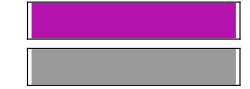

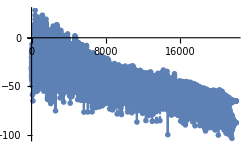

```mathematica
ClearAll["Global`*"]
record1 = Sound[SoundNote["G",1,"Violin"]]
Periodogram[record1]
```

#### Shifting sound by a fixed frequency

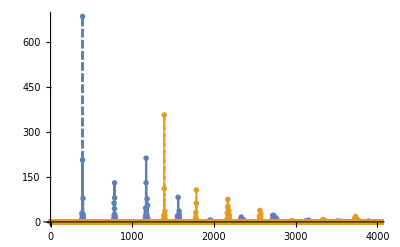

```mathematica
res=AudioFrequencyShift[record1,Quantity[1000,"Hertz"]]

Periodogram[{record1,res},PlotRange->{{0,4000},All},ScalingFunctions->"Absolute"]
```

#### Shifting sound using a given coefficient

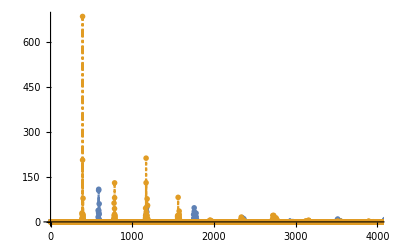

```mathematica
new = AudioPitchShift[record1, 1.5]
Periodogram[{new, record1},PlotRange->{{0,4000},All},ScalingFunctions->"Absolute"]
```